## Wobbling frequency

## Analyzing Ω^4+BΩ^2+C

```mathematica
ClearAll["Global`*"]
```

### Working with (Ā)_k=1/ℐ_0 A_k

```mathematica
bar[I0_,Ak_]:=1/I0 Ak;
(* the intrinsic terms with I *)
Subscript[P, 31][I_,j_,I0_,A1_,A3_]:=(2I-1)(bar[I0,A3]-bar[I0,A1])+2j*bar[I0,A1];
Subscript[P, 21][I_,j_,I0_,A1_,A2_]:=(2I-1)(bar[I0,A2]-bar[I0,A1])+2j*bar[I0,A1];
(* the single-particle terms with j *)
Subscript[Q, 31][I_,j_,I0_,A1_,A3_]:=(2j-1)(bar[I0,A3]-bar[I0,A1])+2I*bar[I0,A1];
Subscript[Q, 21][I_,j_,I0_,A1_,A2_]:=(2j-1)(bar[I0,A2]-bar[I0,A1])+2I*bar[I0,A1];
(* the triaxial terms *)
Subscript[G, 1][j_,γ_]:=((2j-1)/(j(j+1)))Sqrt[3](Sqrt[3]Cos[γ*π/180]+Sin[γ*π/180]);
Subscript[G, 2][j_,γ_]:=((2j-1)/(j(j+1)))2Sqrt[3]Sin[γ*π/180];
```

## Numerical case

```mathematica
Subscript[j, 0]=13/2;
Subscript[γ, 0]=25;
Subscript[ℐ, 0]=42;
Subscript[I, 0]=27/2;
Subscript[A, 1]=0.1;
Subscript[A, 2]=0.3;
Subscript[A, 3]=0.9;
```

```mathematica
Subscript[S, 01][I0_,V_]:=Subscript[P, 31][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]*Subscript[G, 1][Subscript[j, 0],Subscript[γ, 0]]*V+1/I0(Subscript[P, 31][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]*Subscript[Q, 31][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]-4 Subscript[I, 0]*Subscript[j, 0]*bar[Subscript[I, 0],Subscript[A, 3]]^2);
Subscript[S, 02][I0_,V_]:=Subscript[P, 21][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]*Subscript[G, 2][Subscript[j, 0],Subscript[γ, 0]]*V+1/I0(Subscript[P, 21][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]*Subscript[Q, 21][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]-4 Subscript[I, 0]*Subscript[j, 0]*bar[Subscript[I, 0],Subscript[A, 2]]^2);
```

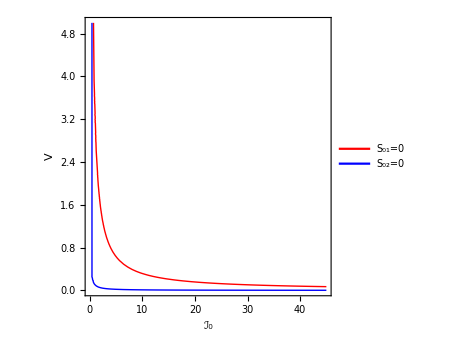

```mathematica
cp1=ContourPlot[{Subscript[S, 01][x,y]==0,Subscript[S, 02][x,y]==0},{x,0,45},{y,0,5},FrameStyle->Directive[Black,Thick],AspectRatio->1,Axes->False,ContourStyle->{{Red,Thick},{Thick,Blue}},FrameLabel->{"ℐ_0","V"},ImageSize->350,LabelStyle->{18,Black,Bold,FontFamily->"Arial"},PlotLegends->Placed[{"S_01=0","S_02=0"},{0.7,0.8}]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/S0102_solutions.pdf",Show[cp1]];
Show[cp1]
```